## Initializing

#### Candidate ranges

from findcriticaleigenvalues (other notebook). Found with ρinf = 20*λ. First three λcs sort of added in there.

```mathematica
ranges={{0.5,1.},{3.,4.},{6.5,7.5},{12.900390625,13.8671875},{19.66796875,20.634765625},{28.369140625,29.3359375},{39.00390625,39.970703125},{50.60546875,51.572265625},{64.140625,65.107421875},{78.642578125,79.609375},{96.044921875,97.01171875},{113.447265625,114.4140625},{133.75,134.716796875},{155.01953125,155.986328125},{178.22265625,179.189453125},{202.392578125,203.359375},{228.49609375,229.462890625},{255.56640625,256.533203125},{285.537109375,286.50390625},{315.5078125,316.474609375},{348.37890625,349.345703125},{382.216796875,383.18359375},{417.98828125,418.955078125},{454.7265625,455.693359375},{493.3984375,494.365234375},{533.037109375,534.00390625},{574.609375,575.576171875},{618.115234375,619.08203125},{663.5546875,664.521484375},{709.9609375,710.927734375},{757.333984375,758.30078125},{807.607421875,808.57421875},{858.84765625,859.814453125},{911.0546875,912.021484375},{965.1953125,966.162109375}};
```

#### Functions for finding λcs

This function pulls out the list of the 25 eigenvalues closest to zero. Around the lower lambdas, that is rough for bisection.

```mathematica
Critical[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=consts[[2]];
nn=consts[[3]];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

This one counts the negative eigenvalues at some λ.

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

This is a bisection routine. It tries to catch when eigenvalues fall off the end by checking to see whether the first eigenvalue at the high end of the range is lower than the first eigenvalue at the low end of the range. This usually means that one was lost.

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,ret},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
(*Print[{lnegs,mnegs},{val[[1]],vam[[1]]}];*)
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]),
Return[Bisect[F,consts,x0,mid,ϵ]];,
Return[Bisect[F,consts,mid,xf,ϵ]];
];,
Return[mid];
]
]
```

This function finds the lambda critical. I use this because I wanted to make sure I was bisecting a range with a root in it.

```mathematica
Findlc[input_,i_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[Ceiling[i,3]/3]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{input[[2,1]],input[[2,2]],input[[2,2]]/input[[2,1]]}];
vah=Critical[input[[4]],{input[[2,1]],input[[2,2]],input[[2,2]]/input[[2,1]]}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={input[[1]],Bisect[Critical,{input[[2,1]],input[[2,2]],input[[2,2]]/input[[2,1]]},input[[3]],input[[4]],10^(-6)]};
,(*else*)
Print["Fail!"];
res={input[[1]],Null};
];
Print[{{val[[1]],lnegs},{vah[[1]],hnegs}}];
Return[res]
]
```

This will be needed later, for folding in recomputed values in the event of a range without a zero.

```mathematica
Merge[a_,b_]:=Module[{vals,res},
res=a;
vals=b;
For[i=1,i≤Length[res],i++,
If[res[[i,2]]==Null,(*if this was a recomputed value*)
res[[i]]=vals[[1]]; (*Slot in the head of the list of recomputed values*)
vals=Delete[vals,1]; (*and delete it, moving the next value to the head*)
];
];
Return[res]
]
```

#### Massaging inputs:

```mathematica
ins={{0.1,80000.},{0.05,160000.}};
```

Making a list of inputs -- {number, ρinf, range low, range high}. Joins done in order to broaden some ranges.

```mathematica
inputs=Join[{Table[{j,ins[[j]],ranges[[1,1]],ranges[[1,2]]},{j,1,2}]},Table[Table[{j,ins[[j]],ranges[[i,1]]-1,ranges[[i,2]]+1},{j,1,2}],{i,2,Length[ranges]}]];
```

```mathematica
inputs = Flatten[inputs, 1]
```

{{1,{0.1,80000.},0.5,1.},{2,{0.05,160000.},0.5,1.},{1,{0.1,80000.},2.,5.},{2,{0.05,160000.},2.,5.},{1,{0.1,80000.},5.5,8.5},{2,{0.05,160000.},5.5,8.5},{1,{0.1,80000.},11.9004,14.8672},{2,{0.05,160000.},11.9004,14.8672},{1,{0.1,80000.},18.668,21.6348},{2,{0.05,160000.},18.668,21.6348},{1,{0.1,80000.},27.3691,30.3359},{2,{0.05,160000.},27.3691,30.3359},{1,{0.1,80000.},38.0039,40.9707},{2,{0.05,160000.},38.0039,40.9707},{1,{0.1,80000.},49.6055,52.5723},{2,{0.05,160000.},49.6055,52.5723},{1,{0.1,80000.},63.1406,66.1074},{2,{0.05,160000.},63.1406,66.1074},{1,{0.1,80000.},77.6426,80.6094},{2,{0.05,160000.},77.6426,80.6094},{1,{0.1,80000.},95.0449,98.0117},{2,{0.05,160000.},95.0449,98.0117},{1,{0.1,80000.},112.447,115.414},{2,{0.05,160000.},112.447,115.414},{1,{0.1,80000.},132.75,135.717},{2,{0.05,160000.},132.75,135.717},{1,{0.1,80000.},154.02,156.986},{2,{0.05,160000.},154.02,156.986},{1,{0.1,80000.},177.223,180.189},{2,{0.05,160000.},177.223,180.189},{1,{0.1,80000.},201.393,204.359},{2,{0.05,160000.},201.393,204.359},{1,{0.1,80000.},227.496,230.463},{2,{0.05,160000.},227.496,230.463},{1,{0.1,80000.},254.566,257.533},{2,{0.05,160000.},254.566,257.533},{1,{0.1,80000.},284.537,287.504},{2,{0.05,160000.},284.537,287.504},{1,{0.1,80000.},314.508,317.475},{2,{0.05,160000.},314.508,317.475},{1,{0.1,80000.},347.379,350.346},{2,{0.05,160000.},347.379,350.346},{1,{0.1,80000.},381.217,384.184},{2,{0.05,160000.},381.217,384.184},{1,{0.1,80000.},416.988,419.955},{2,{0.05,160000.},416.988,419.955},{1,{0.1,80000.},453.727,456.693},{2,{0.05,160000.},453.727,456.693},{1,{0.1,80000.},492.398,495.365},{2,{0.05,160000.},492.398,495.365},{1,{0.1,80000.},532.037,535.004},{2,{0.05,160000.},532.037,535.004},{1,{0.1,80000.},573.609,576.576},{2,{0.05,160000.},573.609,576.576},{1,{0.1,80000.},617.115,620.082},{2,{0.05,160000.},617.115,620.082},{1,{0.1,80000.},662.555,665.521},{2,{0.05,160000.},662.555,665.521},{1,{0.1,80000.},708.961,711.928},{2,{0.05,160000.},708.961,711.928},{1,{0.1,80000.},756.334,759.301},{2,{0.05,160000.},756.334,759.301},{1,{0.1,80000.},806.607,809.574},{2,{0.05,160000.},806.607,809.574},{1,{0.1,80000.},857.848,860.814},{2,{0.05,160000.},857.848,860.814},{1,{0.1,80000.},910.055,913.021},{2,{0.05,160000.},910.055,913.021},{1,{0.1,80000.},964.195,967.162},{2,{0.05,160000.},964.195,967.162}}

## Computation -- TAKES A LONG TIME

```mathematica
len=Length[inputs]
```

70

First, distribute:

```mathematica
DistributeDefinitions[Findlc,Bisect,Critical,CountNegs,inputs,len]
```

Then compute! This is a total of seven computations per core, each of which is 23 bisections. Each bisection calls Critical[] twice and takes roughly 0.11 hours (six minutes, give or take) for the higher value of rhoinf. This means the entire calculation should run in about 24 hours.

```mathematica
lcs=ParallelTable[Findlc[inputs[[i]],i],{i,1,len}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 2th lambda, part 2

***Beginning to calculate the 3th lambda, part 1

***Beginning to calculate the 4th lambda, part 2

***Beginning to calculate the 5th lambda, part 1

***Beginning to calculate the 6th lambda, part 2

***Beginning to calculate the 7th lambda, part 1

***Beginning to calculate the 8th lambda, part 2

***Beginning to calculate the 9th lambda, part 1

***Beginning to calculate the 10th lambda, part 2

Pass!

Bisecting. Midpoint is 79.126

Pass!

Bisecting. Midpoint is 13.3838

Pass!

Bisecting. Midpoint is 134.233

Pass!

Bisecting. Midpoint is 0.75

Pass!

Bisecting. Midpoint is 39.4873

Bisecting. Midpoint is 78.3843

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 78.7551

Bisecting. Midpoint is 133.492

Bisecting. Midpoint is 0.875

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 38.7456

Bisecting. Midpoint is 78.5697

Bisecting. Midpoint is 12.8275

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 133.121

Bisecting. Midpoint is 78.6624

Bisecting. Midpoint is 0.8125

Bisecting. Midpoint is 38.3748

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 78.7088

Bisecting. Midpoint is 132.935

Pass!

Bisecting. Midpoint is 96.5283

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 38.5602

Pass!

Bisecting. Midpoint is 78.7319

Bisecting. Midpoint is 133.028

Bisecting. Midpoint is 0.84375

Pass!

Bisecting. Midpoint is 12.7116

Bisecting. Midpoint is 51.0889

Bisecting. Midpoint is 78.7435

Bisecting. Midpoint is 3.5

Bisecting. Midpoint is 0.828125

Bisecting. Midpoint is 38.6529

Bisecting. Midpoint is 78.7493

Bisecting. Midpoint is 12.7

Bisecting. Midpoint is 132.982

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 78.7522

Bisecting. Midpoint is 12.6942

Bisecting. Midpoint is 0.835938

Bisecting. Midpoint is 38.6065

Bisecting. Midpoint is 78.7508

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 78.7501

Bisecting. Midpoint is 0.839844

Bisecting. Midpoint is 38.6297

Bisecting. Midpoint is 132.993

Bisecting. Midpoint is 12.6899

Bisecting. Midpoint is 78.7504

Bisecting. Midpoint is 95.7866

Bisecting. Midpoint is 12.6892

Bisecting. Midpoint is 78.7506

Bisecting. Midpoint is 0.841797

Bisecting. Midpoint is 132.988

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 2.75

Bisecting. Midpoint is 38.6413

Bisecting. Midpoint is 50.3472

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 132.99

Bisecting. Midpoint is 0.842773

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 12.6894

Bisecting. Midpoint is 38.6471

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 12.6894

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 0.842285

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 38.65

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 132.988

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 0.842529

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 38.6514

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 95.4158

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 0.842651

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 38.6522

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 3.125

Bisecting. Midpoint is 50.718

Bisecting. Midpoint is 0.842712

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 132.989

{{1.51909×10^-9,0},{1.57774×10^-9,0}}

***Beginning to calculate the 7th lambda, part 2

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 38.6525

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 0.842682

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 0.842697

Bisecting. Midpoint is 38.6527

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 132.989

{{1.54057×10^-9,0},{1.54464×10^-9,0}}

***Beginning to calculate the 3th lambda, part 2

Bisecting. Midpoint is 0.84269

Pass!

Bisecting. Midpoint is 79.126

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 95.2303

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 0.842686

Bisecting. Midpoint is 3.3125

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 50.5326

Bisecting. Midpoint is 0.842688

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 38.6526

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 78.3843

Bisecting. Midpoint is 0.842687

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 0.842687

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 95.3231

{{1.54208×10^-9,0},{1.54243×10^-9,0}}

***Beginning to calculate the 1th lambda, part 2

Bisecting. Midpoint is 78.7551

Bisecting. Midpoint is 3.21875

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 19.7689

{{1.21645×10^-9,0},{1.60065×10^-9,0}}

***Beginning to calculate the 9th lambda, part 2

Bisecting. Midpoint is 50.4399

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 78.5697

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 95.2767

Pass!

Bisecting. Midpoint is 0.75

Bisecting. Midpoint is 3.26563

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 78.6624

Pass!

Bisecting. Midpoint is 134.233

{{1.5268×10^-9,0},{1.55361×10^-9,0}}

***Beginning to calculate the 5th lambda, part 2

Bisecting. Midpoint is 50.4862

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 78.7088

Bisecting. Midpoint is 0.875

Bisecting. Midpoint is 95.2535

Bisecting. Midpoint is 3.24219

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 133.492

Bisecting. Midpoint is 78.7319

Pass!

Bisecting. Midpoint is 39.4873

Bisecting. Midpoint is 0.8125

Bisecting. Midpoint is 50.4631

Bisecting. Midpoint is 95.2419

Bisecting. Midpoint is 3.23047

Bisecting. Midpoint is 78.7435

Bisecting. Midpoint is 133.121

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 78.7377

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 0.84375

Bisecting. Midpoint is 95.2477

Bisecting. Midpoint is 3.22461

Bisecting. Midpoint is 78.7406

Bisecting. Midpoint is 132.935

Bisecting. Midpoint is 38.7456

Bisecting. Midpoint is 12.7348

Pass!

Bisecting. Midpoint is 155.503

Bisecting. Midpoint is 19.7704

Bisecting. Midpoint is 50.4515

Bisecting. Midpoint is 0.828125

Bisecting. Midpoint is 95.2448

Bisecting. Midpoint is 78.7421

Bisecting. Midpoint is 3.22168

Bisecting. Midpoint is 133.028

Bisecting. Midpoint is 78.7414

Bisecting. Midpoint is 95.2463

Bisecting. Midpoint is 0.835938

Bisecting. Midpoint is 38.3748

Bisecting. Midpoint is 3.22314

Bisecting. Midpoint is 78.7417

Bisecting. Midpoint is 132.982

Bisecting. Midpoint is 50.4457

Bisecting. Midpoint is 78.7415

Bisecting. Midpoint is 95.247

Bisecting. Midpoint is 0.839844

Bisecting. Midpoint is 19.7711

Bisecting. Midpoint is 3.22388

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 132.959

Bisecting. Midpoint is 78.7416

Bisecting. Midpoint is 38.5602

Bisecting. Midpoint is 0.841797

Bisecting. Midpoint is 78.7417

Bisecting. Midpoint is 95.2474

Bisecting. Midpoint is 3.22424

Bisecting. Midpoint is 50.4428

Bisecting. Midpoint is 19.7707

Bisecting. Midpoint is 12.6653

Bisecting. Midpoint is 132.97

Bisecting. Midpoint is 78.7417

Bisecting. Midpoint is 0.84082

Bisecting. Midpoint is 19.7709

Bisecting. Midpoint is 3.22443

Bisecting. Midpoint is 38.6529

Bisecting. Midpoint is 12.6769

Bisecting. Midpoint is 95.2475

Bisecting. Midpoint is 78.7416

Bisecting. Midpoint is 132.976

Bisecting. Midpoint is 78.7417

Bisecting. Midpoint is 0.840332

Bisecting. Midpoint is 19.771

Bisecting. Midpoint is 3.22433

Bisecting. Midpoint is 50.4413

Bisecting. Midpoint is 95.2475

Bisecting. Midpoint is 12.6827

Bisecting. Midpoint is 78.7417

Bisecting. Midpoint is 0.840576

Bisecting. Midpoint is 38.6065

Bisecting. Midpoint is 132.973

Bisecting. Midpoint is 78.7416

Bisecting. Midpoint is 3.22438

Bisecting. Midpoint is 19.771

Bisecting. Midpoint is 78.7416

Bisecting. Midpoint is 95.2475

Bisecting. Midpoint is 0.840698

Bisecting. Midpoint is 3.2244

Bisecting. Midpoint is 132.972

Bisecting. Midpoint is 78.7416

Bisecting. Midpoint is 38.6297

Bisecting. Midpoint is 0.840637

Bisecting. Midpoint is 19.7709

{{3.82647×10^-10,0},{3.89964×10^-10,0}}

***Beginning to calculate the 7th lambda, part 1

Bisecting. Midpoint is 95.2475

Bisecting. Midpoint is 12.6855

Bisecting. Midpoint is 50.4421

Pass!

Bisecting. Midpoint is 96.5283

Bisecting. Midpoint is 3.22439

Bisecting. Midpoint is 95.7866

Bisecting. Midpoint is 132.972

Bisecting. Midpoint is 95.4158

Bisecting. Midpoint is 95.2303

Bisecting. Midpoint is 95.3231

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 0.840607

Bisecting. Midpoint is 95.2535

Bisecting. Midpoint is 95.2475

Bisecting. Midpoint is 95.2651

Bisecting. Midpoint is 3.2244

Bisecting. Midpoint is 95.2593

Bisecting. Midpoint is 38.6413

Bisecting. Midpoint is 132.972

Bisecting. Midpoint is 95.2564

Bisecting. Midpoint is 95.2579

Bisecting. Midpoint is 19.771

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 95.259

Bisecting. Midpoint is 0.840591

Bisecting. Midpoint is 95.2588

Bisecting. Midpoint is 95.2475

Bisecting. Midpoint is 95.2587

Bisecting. Midpoint is 3.22439

Bisecting. Midpoint is 154.761

Bisecting. Midpoint is 132.972

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 12.687

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 50.4424

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 0.840599

Bisecting. Midpoint is 38.6471

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 95.2475

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 3.22439

Bisecting. Midpoint is 132.972

Bisecting. Midpoint is 95.2586

{{1.31465×10^-9,0},{1.57857×10^-9,0}}

***Beginning to calculate the 11th lambda, part 1

Fail!

{{-1.90178×10^-10,1},{-4.70823×10^-7,1}}

***Beginning to calculate the 11th lambda, part 2

Bisecting. Midpoint is 19.7709

Bisecting. Midpoint is 0.840603

Bisecting. Midpoint is 95.2475

Fail!

{{-3.12463×10^-10,1},{3.97706×10^-10,0}}

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 12.6863

Bisecting. Midpoint is 3.22439

Fail!

{{-2.26689×10^-9,1},{-3.65525×10^-7,1}}

***Beginning to calculate the 12th lambda, part 2

Bisecting. Midpoint is 132.972

Fail!

{{-2.31088×10^-9,1},{3.99474×10^-10,0}}

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 38.65

Bisecting. Midpoint is 0.840605

Pass!

Bisecting. Midpoint is 256.05

Bisecting. Midpoint is 255.308

Bisecting. Midpoint is 95.2475

Bisecting. Midpoint is 254.937

Bisecting. Midpoint is 3.22439

Bisecting. Midpoint is 254.752

Bisecting. Midpoint is 132.972

Bisecting. Midpoint is 19.771

Bisecting. Midpoint is 50.4422

Bisecting. Midpoint is 254.845

Bisecting. Midpoint is 254.798

Bisecting. Midpoint is 254.821

Bisecting. Midpoint is 254.81

Bisecting. Midpoint is 0.840606

Bisecting. Midpoint is 254.816

Bisecting. Midpoint is 95.2475

Bisecting. Midpoint is 254.818

{{3.8556×10^-10,0},{3.85601×10^-10,0}}

***Beginning to calculate the 2th lambda, part 1

Bisecting. Midpoint is 132.972

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 254.821

Pass!

Bisecting. Midpoint is 7.

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 7.75

Bisecting. Midpoint is 38.6485

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 0.840606

Bisecting. Midpoint is 50.4421

Bisecting. Midpoint is 7.375

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 12.6866

{{3.54589×10^-10,0},{3.90068×10^-10,0}}

***Beginning to calculate the 8th lambda, part 1

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 132.972

Bisecting. Midpoint is 7.1875

Bisecting. Midpoint is 254.82

Pass!

Bisecting. Midpoint is 113.931

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 7.09375

Bisecting. Midpoint is 113.189

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 19.771

Bisecting. Midpoint is 113.56

Bisecting. Midpoint is 7.14063

Bisecting. Midpoint is 254.82

{{3.85548×10^-10,0},{3.85591×10^-10,0}}

***Beginning to calculate the 1th lambda, part 1

Bisecting. Midpoint is 113.374

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 7.16406

{{8.71209×10^-10,0},{-1.9488×10^-7,1}}

***Beginning to calculate the 12th lambda, part 2

Bisecting. Midpoint is 132.972

Bisecting. Midpoint is 113.282

Pass!

Bisecting. Midpoint is 3.5

Bisecting. Midpoint is 7.17578

Bisecting. Midpoint is 113.328

Bisecting. Midpoint is 2.75

Bisecting. Midpoint is 12.6868

Bisecting. Midpoint is 7.16992

Pass!

Bisecting. Midpoint is 256.05

Bisecting. Midpoint is 3.125

Bisecting. Midpoint is 113.351

Bisecting. Midpoint is 7.17285

Bisecting. Midpoint is 38.6478

Bisecting. Midpoint is 3.3125

Bisecting. Midpoint is 113.34

Bisecting. Midpoint is 7.17432

Bisecting. Midpoint is 255.308

Bisecting. Midpoint is 3.21875

Bisecting. Midpoint is 7.17358

Bisecting. Midpoint is 113.334

Bisecting. Midpoint is 132.972

Bisecting. Midpoint is 3.26563

Bisecting. Midpoint is 7.17395

Bisecting. Midpoint is 113.337

Bisecting. Midpoint is 3.24219

Bisecting. Midpoint is 254.937

Bisecting. Midpoint is 7.17413

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 50.4421

Bisecting. Midpoint is 3.23047

Bisecting. Midpoint is 7.17422

Bisecting. Midpoint is 113.337

Bisecting. Midpoint is 3.22461

Bisecting. Midpoint is 7.17418

Bisecting. Midpoint is 254.752

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 3.22754

Bisecting. Midpoint is 7.1742

Bisecting. Midpoint is 12.6869

Bisecting. Midpoint is 19.7709

Bisecting. Midpoint is 132.972

Bisecting. Midpoint is 3.22607

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 7.17421

Bisecting. Midpoint is 254.845

Bisecting. Midpoint is 3.22681

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 7.17422

Bisecting. Midpoint is 38.6482

Bisecting. Midpoint is 3.22644

Bisecting. Midpoint is 7.17422

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 254.798

Bisecting. Midpoint is 3.22662

Bisecting. Midpoint is 7.17422

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.687

Bisecting. Midpoint is 3.22653

Bisecting. Midpoint is 7.17422

Bisecting. Midpoint is 132.972

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 254.775

Bisecting. Midpoint is 3.22658

Bisecting. Midpoint is 7.17422

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 3.2266

{{1.54234×10^-9,0},{1.54365×10^-9,0}}

***Beginning to calculate the 2th lambda, part 2

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 3.22659

Bisecting. Midpoint is 254.787

Bisecting. Midpoint is 50.4421

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 3.22658

Bisecting. Midpoint is 3.22658

Bisecting. Midpoint is 254.781

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 154.39

{{3.39289×10^-10,0},{3.92765×10^-10,0}}

***Beginning to calculate the 9th lambda, part 1

Bisecting. Midpoint is 3.22658

Bisecting. Midpoint is 113.338

Pass!

Bisecting. Midpoint is 7.

Pass!

Bisecting. Midpoint is 155.503

Bisecting. Midpoint is 3.22658

{{1.4833×10^-9,0},{1.59765×10^-9,0}}

***Beginning to calculate the 8th lambda, part 2

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 154.761

Bisecting. Midpoint is 38.6484

Bisecting. Midpoint is 3.22658

Bisecting. Midpoint is 19.7709

Bisecting. Midpoint is 154.39

Bisecting. Midpoint is 12.687

{{1.54218×10^-9,0},{1.5425×10^-9,0}}

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 154.205

Bisecting. Midpoint is 254.776

Fail!

{{-9.59002×10^-9,1},{-2.45945×10^-7,1}}

***Beginning to calculate the 13th lambda, part 2

Bisecting. Midpoint is 154.298

Bisecting. Midpoint is 7.75

Bisecting. Midpoint is 154.251

Pass!

Bisecting. Midpoint is 113.931

Bisecting. Midpoint is 254.777

Bisecting. Midpoint is 154.228

Bisecting. Midpoint is 154.217

Fail!

{{-9.64716×10^-9,1},{-2.46236×10^-7,1}}

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 50.4421

Bisecting. Midpoint is 154.211

Bisecting. Midpoint is 254.778

Pass!

Bisecting. Midpoint is 315.991

Bisecting. Midpoint is 154.214

Bisecting. Midpoint is 7.375

Bisecting. Midpoint is 113.189

Bisecting. Midpoint is 315.25

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 314.879

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 154.211

Bisecting. Midpoint is 314.693

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 314.601

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 314.554

Bisecting. Midpoint is 7.1875

Bisecting. Midpoint is 113.56

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 38.6483

Bisecting. Midpoint is 314.577

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 12.687

Bisecting. Midpoint is 314.566

{{3.8534×10^-10,0},{3.86194×10^-10,0}}

***Beginning to calculate the 4th lambda, part 1

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 314.56

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 314.557

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 113.374

Bisecting. Midpoint is 314.559

Bisecting. Midpoint is 7.09375

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 314.558

Pass!

Bisecting. Midpoint is 28.8525

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 314.557

Bisecting. Midpoint is 12.687

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 50.4421

Bisecting. Midpoint is 28.1108

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 314.558

Bisecting. Midpoint is 28.4817

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 28.2963

Bisecting. Midpoint is 314.558

Bisecting. Midpoint is 113.282

Bisecting. Midpoint is 28.389

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 38.6482

{{1.06472×10^-9,0},{-8.9975×10^-7,1}}

***Beginning to calculate the 14th lambda, part 1

Bisecting. Midpoint is 314.558

Bisecting. Midpoint is 7.14063

Bisecting. Midpoint is 12.687

Bisecting. Midpoint is 28.4353

Bisecting. Midpoint is 314.558

Fail!

{{-5.14716×10^-9,1},{-1.33973×10^-7,1}}

***Beginning to calculate the 14th lambda, part 2

Bisecting. Midpoint is 28.4122

Bisecting. Midpoint is 28.4237

Bisecting. Midpoint is 314.558

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 28.4295

Bisecting. Midpoint is 314.558

Bisecting. Midpoint is 28.4266

Bisecting. Midpoint is 12.687

Bisecting. Midpoint is 314.558

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 113.328

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 28.4288

Bisecting. Midpoint is 7.16406

Bisecting. Midpoint is 314.558

Fail!

{{-5.17834×10^-9,1},{-1.34131×10^-7,1}}

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 28.4285

Bisecting. Midpoint is 314.558

Bisecting. Midpoint is 28.4283

Fail!

{{-4.53226×10^-9,1},{-1.04361×10^-7,1}}

***Beginning to calculate the 15th lambda, part 2

Bisecting. Midpoint is 12.687

Bisecting. Midpoint is 314.558

Bisecting. Midpoint is 28.4282

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 28.4281

{{2.01063×10^-10,0},{-1.2118×10^-7,1}}

***Beginning to calculate the 14th lambda, part 2

Bisecting. Midpoint is 50.4421

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 38.6482

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 113.305

Bisecting. Midpoint is 7.17578

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 12.687

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 28.4281

Fail!

{{-4.55795×10^-9,1},{-1.04483×10^-7,1}}

***Beginning to calculate the 15th lambda, part 1

Fail!

{{-1.9206×10^-11,1},{-1.21355×10^-7,1}}

***Beginning to calculate the 16th lambda, part 1

Bisecting. Midpoint is 28.4281

{{2.68366×10^-10,0},{-1.95185×10^-7,1}}

***Beginning to calculate the 17th lambda, part 1

Fail!

{{-4.55744×10^-9,1},{-6.97812×10^-8,1}}

***Beginning to calculate the 16th lambda, part 2

Fail!

{{-4.92924×10^-9,1},{-5.95663×10^-8,1}}

***Beginning to calculate the 17th lambda, part 2

Fail!

{{-8.20381×10^-9,1},{-9.871×10^-8,1}}

***Beginning to calculate the 16th lambda, part 2

Bisecting. Midpoint is 28.4281

{{3.85358×10^-10,0},{3.85868×10^-10,0}}

***Beginning to calculate the 3th lambda, part 1

{{1.53822×10^-9,0},{1.55052×10^-9,0}}

***Beginning to calculate the 4th lambda, part 2

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 7.16992

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 113.316

Fail!

{{-4.94747×10^-9,1},{-5.96288×10^-8,1}}

***Beginning to calculate the 17th lambda, part 1

Fail!

{{-1.61109×10^-9,1},{-3.79156×10^-8,1}}

***Beginning to calculate the 18th lambda, part 2

Bisecting. Midpoint is 19.7805

Fail!

{{-4.57737×10^-9,1},{-6.98577×10^-8,1}}

***Beginning to calculate the 18th lambda, part 1

Fail!

{{-8.23347×10^-9,1},{-9.88135×10^-8,1}}

***Beginning to calculate the 19th lambda, part 1

Fail!

{{-1.06829×10^-9,1},{-2.92059×10^-8,1}}

***Beginning to calculate the 18th lambda, part 2

Bisecting. Midpoint is 19.5951

Fail!

{{-1.63377×10^-9,1},{-3.79598×10^-8,1}}

***Beginning to calculate the 19th lambda, part 1

Bisecting. Midpoint is 7.17285

Fail!

{{-1.77139×10^-9,1},{-2.74496×10^-8,1}}

***Beginning to calculate the 19th lambda, part 2

Bisecting. Midpoint is 38.6482

Fail!

{{-3.94728×10^-9,1},{-3.02445×10^-8,1}}

***Beginning to calculate the 20th lambda, part 2

Bisecting. Midpoint is 50.4421

Pass!

Bisecting. Midpoint is 28.8525

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 113.322

Fail!

{{-1.104×10^-9,1},{-2.92405×10^-8,1}}

Fail!

{{-3.9586×10^-9,1},{-3.02728×10^-8,1}}

***Beginning to calculate the 20th lambda, part 1

***Beginning to calculate the 21th lambda, part 1

Bisecting. Midpoint is 19.7342

Fail!

{{-1.31829×10^-9,1},{-1.62311×10^-8,1}}

***Beginning to calculate the 21th lambda, part 2

Bisecting. Midpoint is 19.7573

Fail!

{{-3.4519×10^-9,1},{-2.52923×10^-8,1}}

***Beginning to calculate the 20th lambda, part 2

Fail!

{{-1.79063×10^-9,1},{-2.74797×10^-8,1}}

Bisecting. Midpoint is 19.7689

***Beginning to calculate the 21th lambda, part 1

Bisecting. Midpoint is 7.17139

Bisecting. Midpoint is 28.1108

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 154.205

Fail!

{{-3.03482×10^-9,1},{-1.8944×10^-8,1}}

***Beginning to calculate the 22th lambda, part 2

Bisecting. Midpoint is 113.325

Bisecting. Midpoint is 19.7718

Fail!

{{-1.34567×10^-9,1},{-1.6248×10^-8,1}}

***Beginning to calculate the 22th lambda, part 1

Fail!

{{-3.00487×10^-9,1},{-1.69131×10^-8,1}}

***Beginning to calculate the 22th lambda, part 2

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 38.6482

Fail!

{{-3.46241×10^-9,1},{-2.53157×10^-8,1}}

***Beginning to calculate the 23th lambda, part 1

Bisecting. Midpoint is 19.774

Bisecting. Midpoint is 28.4817

Bisecting. Midpoint is 19.7736

Fail!

{{-1.61277×10^-9,1},{-1.1896×10^-8,1}}

***Beginning to calculate the 23th lambda, part 2

Fail!

{{-3.01428×10^-9,1},{-1.69275×10^-8,1}}

***Beginning to calculate the 23th lambda, part 1

Bisecting. Midpoint is 7.17212

Bisecting. Midpoint is 19.7738

Fail!

{{-3.04462×10^-9,1},{-1.89606×10^-8,1}}

Fail!

{{-1.25009×10^-9,1},{-9.73804×10^-9,1}}

***Beginning to calculate the 24th lambda, part 2

Bisecting. Midpoint is 113.324

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 50.4421

Bisecting. Midpoint is 19.774

Bisecting. Midpoint is 28.2963

Bisecting. Midpoint is 19.7739

Fail!

{{-1.28086×10^-9,1},{-9.74714×10^-9,1}}

Bisecting. Midpoint is 19.7739

Fail!

{{-1.63365×10^-9,1},{-1.1907×10^-8,1}}

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 7.17175

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 28.389

Bisecting. Midpoint is 113.324

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 38.6482

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 28.4353

{{1.54043×10^-9,0},{1.54726×10^-9,0}}

Bisecting. Midpoint is 7.17194

Bisecting. Midpoint is 113.324

Bisecting. Midpoint is 28.4122

Bisecting. Midpoint is 50.4421

Bisecting. Midpoint is 113.324

Bisecting. Midpoint is 28.4237

Bisecting. Midpoint is 7.17184

Bisecting. Midpoint is 38.6482

Bisecting. Midpoint is 28.4295

Bisecting. Midpoint is 113.324

Bisecting. Midpoint is 7.17189

Bisecting. Midpoint is 28.4266

Bisecting. Midpoint is 113.324

{{3.83486×10^-10,0},{3.87733×10^-10,0}}

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 28.4252

Bisecting. Midpoint is 7.17191

Bisecting. Midpoint is 38.6482

Pass!

Bisecting. Midpoint is 64.624

Bisecting. Midpoint is 63.8823

Bisecting. Midpoint is 28.4245

Bisecting. Midpoint is 63.5115

Bisecting. Midpoint is 113.324

Bisecting. Midpoint is 63.6969

Bisecting. Midpoint is 7.1719

Bisecting. Midpoint is 28.4248

Bisecting. Midpoint is 38.6482

Bisecting. Midpoint is 63.7896

Bisecting. Midpoint is 63.836

Bisecting. Midpoint is 113.324

Bisecting. Midpoint is 28.4246

Bisecting. Midpoint is 63.8128

Bisecting. Midpoint is 7.1719

Bisecting. Midpoint is 63.8244

Bisecting. Midpoint is 28.4246

Bisecting. Midpoint is 63.8186

Bisecting. Midpoint is 113.324

{{3.83622×10^-10,0},{3.86984×10^-10,0}}

***Beginning to calculate the 5th lambda, part 1

Bisecting. Midpoint is 63.8157

Pass!

Bisecting. Midpoint is 51.0889

Bisecting. Midpoint is 7.1719

Bisecting. Midpoint is 63.8142

Bisecting. Midpoint is 28.4246

Bisecting. Midpoint is 50.3472

Bisecting. Midpoint is 63.8135

Bisecting. Midpoint is 50.718

Bisecting. Midpoint is 113.324

Bisecting. Midpoint is 63.8139

Bisecting. Midpoint is 50.5326

Bisecting. Midpoint is 28.4246

Bisecting. Midpoint is 63.8137

Bisecting. Midpoint is 7.1719

Bisecting. Midpoint is 50.4399

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 50.4862

Bisecting. Midpoint is 113.324

Bisecting. Midpoint is 28.4246

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 50.4631

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 50.4515

Bisecting. Midpoint is 7.1719

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 28.4246

Bisecting. Midpoint is 154.112

Bisecting. Midpoint is 50.4457

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 113.324

Bisecting. Midpoint is 50.4486

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 50.4471

Bisecting. Midpoint is 28.4246

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 50.4478

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 7.1719

Bisecting. Midpoint is 50.4475

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 113.324

Bisecting. Midpoint is 28.4246

Bisecting. Midpoint is 50.4477

{{1.50877×10^-9,0},{1.56536×10^-9,0}}

***Beginning to calculate the 6th lambda, part 2

Bisecting. Midpoint is 50.4478

Bisecting. Midpoint is 28.4246

{{3.8558×10^-10,0},{3.85744×10^-10,0}}

Bisecting. Midpoint is 50.4477

{{3.78052×10^-10,0},{3.92399×10^-10,0}}

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 28.4246

Bisecting. Midpoint is 50.4477

Pass!

Bisecting. Midpoint is 64.624

Bisecting. Midpoint is 50.4477

{{3.85063×10^-10,0},{3.866×10^-10,0}}

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 63.8823

Bisecting. Midpoint is 50.4477

{{1.52571×10^-9,0},{1.55965×10^-9,0}}

Bisecting. Midpoint is 63.5115

Bisecting. Midpoint is 63.6969

Bisecting. Midpoint is 63.7896

Bisecting. Midpoint is 63.836

Bisecting. Midpoint is 63.8128

Bisecting. Midpoint is 63.8012

Bisecting. Midpoint is 63.807

Bisecting. Midpoint is 154.159

Bisecting. Midpoint is 63.8041

Bisecting. Midpoint is 63.8055

Bisecting. Midpoint is 63.8063

Bisecting. Midpoint is 63.8066

Bisecting. Midpoint is 63.8065

Bisecting. Midpoint is 63.8065

Bisecting. Midpoint is 63.8066

Bisecting. Midpoint is 63.8066

Bisecting. Midpoint is 63.8066

«2 more identical outputs»

Bisecting. Midpoint is 154.182

Bisecting. Midpoint is 63.8066

Bisecting. Midpoint is 63.8066

Bisecting. Midpoint is 63.8066

{{3.81329×10^-10,0},{3.8844×10^-10,0}}

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 154.188

Bisecting. Midpoint is 154.19

Bisecting. Midpoint is 154.192

Bisecting. Midpoint is 154.191

Bisecting. Midpoint is 154.191

Bisecting. Midpoint is 154.191

«9 more identical outputs»

{{3.12024×10^-10,0},{3.94322×10^-10,0}}

***Beginning to calculate the 10th lambda, part 1

Fail!

{{-5.21453×10^-9,1},{-7.81999×10^-7,1}}

***Beginning to calculate the 10th lambda, part 2

Fail!

{{-5.30108×10^-9,1},{3.95328×10^-10,0}}

{{1,0.842687},{2,0.840606},{1,3.22658},{2,3.22439},{1,7.17422},{2,7.1719},{1,12.6895},{2,12.687},{1,19.7739},{2,19.7709},{1,28.4281},{2,28.4246},{1,38.6526},{2,38.6482},{1,50.4477},{2,50.4421},{1,63.8136},{2,63.8066},{1,78.7505},{2,78.7416},{1,95.2586},{2,95.2475},{1,113.338},{2,113.324},{1,132.989},{2,132.972},{1,154.212},{2,154.191},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,254.82},{2,254.778},{1,Null},{2,Null},{1,314.558},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null}}

Find all the ones which were missed and then expand their ranges.

```mathematica
lcs={{1,0.8426871299743652},{2,0.8406062126159668},{1,3.226578116416931},{2,3.2243930101394653},{1,7.174222350120544},{2,7.171901345252991},{1,12.689524383982643},{2,12.686958156293258},{1,19.773917039623484},{2,19.770949750440195},{1,28.428132182219997},{2,28.42456082510762},{1,38.652617557672784},{2,38.64820022252388},{1,50.44768833811395},{2,50.44213713775389},{1,63.81358461291529},{2,63.80656921979971},{1,78.75050342851318},{2,78.74164824537002},{1,95.25861514895223},{2,95.2474993087817},{1,113.3380695336964},{2,113.32422760711052},{1,132.98900753981434},{2,132.97192529099993},{1,154.2115601298865},{2,154.1906752239447},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,254.8203860449139},{2,254.7776627393905},{1,Null},{2,Null},{1,314.5576463358011},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null},{1,Null},{2,Null}};
```

```mathematica
missed={};
For[i=1,i≤Length[lcs],i++,
If[lcs[[i,2]]==Null,
missed=Append[missed,i]
]
]
```

```mathematica
missed
```

{45,46,50,57,58,59,60,63,64,65,66,67,68,69,70}

This creates a table with only the inputs where an eigenvalue was not found in the range.

```mathematica
newins=Table[{inputs[[missed[[i]],1]],inputs[[missed[[i]],2]],inputs[[missed[[i]],3]]-2,inputs[[missed[[i]],4]]+2},{i,1,Length[missed]}]
```

{{1,{0.1,80000.},414.988,421.955},{2,{0.05,160000.},414.988,421.955},{2,{0.05,160000.},490.398,497.365},{1,{0.1,80000.},660.555,667.521},{2,{0.05,160000.},660.555,667.521},{1,{0.1,80000.},706.961,713.928},{2,{0.05,160000.},706.961,713.928},{1,{0.1,80000.},804.607,811.574},{2,{0.05,160000.},804.607,811.574},{1,{0.1,80000.},855.848,862.814},{2,{0.05,160000.},855.848,862.814},{1,{0.1,80000.},908.055,915.021},{2,{0.05,160000.},908.055,915.021},{1,{0.1,80000.},962.195,969.162},{2,{0.05,160000.},962.195,969.162}}

We then rerun the computation with those inputs:

```mathematica
DistributeDefinitions[newins]
```

```mathematica
missedlcs=ParallelTable[Findlc[newins[[i]],i],{i,1,Length[newins]}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 1th lambda, part 2

***Beginning to calculate the 2th lambda, part 2

***Beginning to calculate the 3th lambda, part 2

***Beginning to calculate the 3th lambda, part 2

***Beginning to calculate the 4th lambda, part 2

***Beginning to calculate the 5th lambda, part 2

***Beginning to calculate the 5th lambda, part 2

***Beginning to calculate the 5th lambda, part 1

Pass!

Bisecting. Midpoint is 418.472

Bisecting. Midpoint is 416.73

Bisecting. Midpoint is 415.859

Pass!

Bisecting. Midpoint is 493.882

Pass!

Bisecting. Midpoint is 664.038

Bisecting. Midpoint is 416.295

Pass!

Bisecting. Midpoint is 965.679

Pass!

Bisecting. Midpoint is 965.679

Bisecting. Midpoint is 416.077

Pass!

Pass!

Bisecting. Midpoint is 710.444

Bisecting. Midpoint is 859.331

Bisecting. Midpoint is 415.968

Bisecting. Midpoint is 415.914

Bisecting. Midpoint is 963.937

Bisecting. Midpoint is 708.703

Bisecting. Midpoint is 492.14

Bisecting. Midpoint is 662.296

Bisecting. Midpoint is 415.941

Bisecting. Midpoint is 415.954

Bisecting. Midpoint is 707.832

Bisecting. Midpoint is 415.961

Bisecting. Midpoint is 415.958

Bisecting. Midpoint is 857.589

Bisecting. Midpoint is 491.269

Bisecting. Midpoint is 661.426

Bisecting. Midpoint is 415.956

Bisecting. Midpoint is 415.957

Bisecting. Midpoint is 707.396

Bisecting. Midpoint is 963.937

Bisecting. Midpoint is 415.957

Bisecting. Midpoint is 415.957

Bisecting. Midpoint is 856.719

Bisecting. Midpoint is 660.99

Bisecting. Midpoint is 491.705

Bisecting. Midpoint is 415.957

Bisecting. Midpoint is 707.614

Bisecting. Midpoint is 415.957

Pass!

Bisecting. Midpoint is 911.538

Bisecting. Midpoint is 415.957

Bisecting. Midpoint is 856.283

Bisecting. Midpoint is 963.066

Bisecting. Midpoint is 661.208

Bisecting. Midpoint is 415.957

Bisecting. Midpoint is 491.487

Bisecting. Midpoint is 707.505

Bisecting. Midpoint is 415.957

Bisecting. Midpoint is 415.957

Bisecting. Midpoint is 856.065

Bisecting. Midpoint is 962.631

Bisecting. Midpoint is 415.957

Bisecting. Midpoint is 661.099

Bisecting. Midpoint is 415.957

Bisecting. Midpoint is 491.378

Bisecting. Midpoint is 707.451

Bisecting. Midpoint is 415.957

Bisecting. Midpoint is 962.848

{{1.14899×10^-9,0},{-2.1602×10^-7,1}}

***Beginning to calculate the 1th lambda, part 2

Bisecting. Midpoint is 855.957

Bisecting. Midpoint is 707.424

Bisecting. Midpoint is 661.045

Bisecting. Midpoint is 491.324

Bisecting. Midpoint is 962.74

Bisecting. Midpoint is 855.902

Pass!

Bisecting. Midpoint is 418.472

Bisecting. Midpoint is 707.41

Bisecting. Midpoint is 661.017

Bisecting. Midpoint is 491.297

Bisecting. Midpoint is 855.929

Bisecting. Midpoint is 707.403

Bisecting. Midpoint is 416.73

Bisecting. Midpoint is 661.031

Bisecting. Midpoint is 491.31

Bisecting. Midpoint is 962.794

Bisecting. Midpoint is 707.407

Bisecting. Midpoint is 855.943

Bisecting. Midpoint is 415.859

Bisecting. Midpoint is 661.038

Bisecting. Midpoint is 707.408

Bisecting. Midpoint is 962.821

Bisecting. Midpoint is 855.936

Bisecting. Midpoint is 491.303

Bisecting. Midpoint is 707.407

Bisecting. Midpoint is 416.295

Bisecting. Midpoint is 855.933

Bisecting. Midpoint is 661.041

Bisecting. Midpoint is 707.408

Bisecting. Midpoint is 491.307

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 963.066

Bisecting. Midpoint is 962.808

Bisecting. Midpoint is 416.077

Bisecting. Midpoint is 661.043

Bisecting. Midpoint is 707.408

Bisecting. Midpoint is 491.305

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 909.796

Bisecting. Midpoint is 415.968

Bisecting. Midpoint is 661.044

Bisecting. Midpoint is 962.814

Bisecting. Midpoint is 491.306

Bisecting. Midpoint is 415.914

Bisecting. Midpoint is 707.408

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 962.811

Bisecting. Midpoint is 661.043

Bisecting. Midpoint is 491.306

Bisecting. Midpoint is 415.886

Bisecting. Midpoint is 707.408

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 962.813

Bisecting. Midpoint is 661.043

Bisecting. Midpoint is 963.502

Bisecting. Midpoint is 491.306

Bisecting. Midpoint is 415.873

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 707.408

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 661.043

Bisecting. Midpoint is 707.408

Bisecting. Midpoint is 491.306

Bisecting. Midpoint is 415.866

Bisecting. Midpoint is 962.812

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 707.408

Bisecting. Midpoint is 661.043

Bisecting. Midpoint is 415.869

Bisecting. Midpoint is 491.306

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 963.284

Bisecting. Midpoint is 707.408

Bisecting. Midpoint is 661.043

Bisecting. Midpoint is 962.812

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 963.175

Bisecting. Midpoint is 491.306

Bisecting. Midpoint is 963.121

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 963.148

Bisecting. Midpoint is 707.408

Bisecting. Midpoint is 661.043

Bisecting. Midpoint is 963.161

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 962.813

Bisecting. Midpoint is 491.306

Bisecting. Midpoint is 707.408

Bisecting. Midpoint is 908.926

Bisecting. Midpoint is 963.155

Bisecting. Midpoint is 661.043

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 491.306

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 963.151

Bisecting. Midpoint is 707.408

Bisecting. Midpoint is 661.043

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 963.15

{{1.88141×10^-10,0},{-5.14188×10^-8,1}}

***Beginning to calculate the 3th lambda, part 1

Bisecting. Midpoint is 491.306

Pass!

Bisecting. Midpoint is 808.091

Bisecting. Midpoint is 962.813

Bisecting. Midpoint is 806.349

Bisecting. Midpoint is 805.478

Bisecting. Midpoint is 855.934

Bisecting. Midpoint is 805.043

Bisecting. Midpoint is 661.043

Bisecting. Midpoint is 805.261

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 805.152

Bisecting. Midpoint is 491.306

Bisecting. Midpoint is 963.149

Bisecting. Midpoint is 805.097

{{3.96082×10^-11,0},{-3.27093×10^-8,1}}

***Beginning to calculate the 4th lambda, part 1

Bisecting. Midpoint is 908.49

Bisecting. Midpoint is 805.124

Bisecting. Midpoint is 661.043

Pass!

Bisecting. Midpoint is 808.091

Pass!

Bisecting. Midpoint is 911.538

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 805.111

Bisecting. Midpoint is 909.796

Bisecting. Midpoint is 805.104

Bisecting. Midpoint is 908.926

Bisecting. Midpoint is 491.306

Bisecting. Midpoint is 805.101

Bisecting. Midpoint is 908.49

Bisecting. Midpoint is 805.102

Bisecting. Midpoint is 908.708

Bisecting. Midpoint is 805.103

Bisecting. Midpoint is 908.817

Bisecting. Midpoint is 805.104

Bisecting. Midpoint is 908.871

Bisecting. Midpoint is 661.043

Bisecting. Midpoint is 908.898

Bisecting. Midpoint is 805.104

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 908.885

Bisecting. Midpoint is 805.104

Bisecting. Midpoint is 962.813

Bisecting. Midpoint is 806.349

Bisecting. Midpoint is 908.892

Bisecting. Midpoint is 491.306

Bisecting. Midpoint is 805.104

Bisecting. Midpoint is 908.895

Bisecting. Midpoint is 805.104

Bisecting. Midpoint is 908.893

Bisecting. Midpoint is 963.149

Bisecting. Midpoint is 805.104

Bisecting. Midpoint is 908.892

Bisecting. Midpoint is 908.893

Bisecting. Midpoint is 805.104

Bisecting. Midpoint is 805.478

Bisecting. Midpoint is 908.893

Bisecting. Midpoint is 805.104

{{2.09668×10^-10,0},{-6.19606×10^-8,1}}

***Beginning to calculate the 2th lambda, part 1

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 908.893

Bisecting. Midpoint is 805.104

Bisecting. Midpoint is 908.893

Bisecting. Midpoint is 805.104

{{3.13399×10^-10,0},{-1.3059×10^-7,1}}

***Beginning to calculate the 2th lambda, part 1

Pass!

Bisecting. Midpoint is 710.444

Bisecting. Midpoint is 908.893

Bisecting. Midpoint is 805.043

Bisecting. Midpoint is 805.104

Bisecting. Midpoint is 908.893

Bisecting. Midpoint is 708.703

Pass!

Bisecting. Midpoint is 664.038

{{4.52069×10^-10,0},{-3.73736×10^-8,1}}

Bisecting. Midpoint is 908.893

Bisecting. Midpoint is 908.893

Bisecting. Midpoint is 662.296

Bisecting. Midpoint is 707.832

Bisecting. Midpoint is 963.149

Bisecting. Midpoint is 962.813

Bisecting. Midpoint is 908.893

Bisecting. Midpoint is 804.825

Bisecting. Midpoint is 908.893

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 661.426

Bisecting. Midpoint is 707.396

Bisecting. Midpoint is 908.893

{{5.95581×10^-10,0},{-2.4162×10^-8,1}}

Bisecting. Midpoint is 660.99

Bisecting. Midpoint is 707.614

Bisecting. Midpoint is 963.149

Bisecting. Midpoint is 804.934

Bisecting. Midpoint is 661.208

Bisecting. Midpoint is 707.505

Bisecting. Midpoint is 963.149

Bisecting. Midpoint is 661.317

Bisecting. Midpoint is 707.56

Bisecting. Midpoint is 804.88

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 661.262

Bisecting. Midpoint is 707.587

Bisecting. Midpoint is 661.235

Bisecting. Midpoint is 707.6

Bisecting. Midpoint is 804.852

Bisecting. Midpoint is 661.221

Bisecting. Midpoint is 962.813

Bisecting. Midpoint is 707.607

Bisecting. Midpoint is 661.228

Bisecting. Midpoint is 707.611

Bisecting. Midpoint is 804.866

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 661.225

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 661.227

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 804.859

Bisecting. Midpoint is 661.227

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 661.227

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 804.856

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 661.227

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 962.813

Bisecting. Midpoint is 908.708

Bisecting. Midpoint is 661.227

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 804.854

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 661.227

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 661.227

Bisecting. Midpoint is 804.853

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 415.868

Bisecting. Midpoint is 661.227

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 804.853

Bisecting. Midpoint is 661.227

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 661.227

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 804.853

Bisecting. Midpoint is 661.227

{{3.26999×10^-10,0},{-2.16174×10^-7,1}}

Bisecting. Midpoint is 707.612

Bisecting. Midpoint is 661.227

{{6.35708×10^-10,0},{-5.13853×10^-8,1}}

Bisecting. Midpoint is 804.853

Bisecting. Midpoint is 661.227

{{6.92975×10^-10,0},{-6.19199×10^-8,1}}

Bisecting. Midpoint is 804.853

Bisecting. Midpoint is 804.853

Bisecting. Midpoint is 804.853

Bisecting. Midpoint is 962.813

Bisecting. Midpoint is 804.853

Bisecting. Midpoint is 804.853

Bisecting. Midpoint is 908.599

Bisecting. Midpoint is 804.853

Bisecting. Midpoint is 804.853

Bisecting. Midpoint is 804.853

Bisecting. Midpoint is 962.813

{{1.07486×10^-10,0},{-3.7397×10^-8,1}}

***Beginning to calculate the 4th lambda, part 1

Pass!

Bisecting. Midpoint is 859.331

Bisecting. Midpoint is 857.589

Bisecting. Midpoint is 856.719

Bisecting. Midpoint is 856.283

Bisecting. Midpoint is 856.065

Bisecting. Midpoint is 856.174

Bisecting. Midpoint is 856.229

Bisecting. Midpoint is 856.201

Bisecting. Midpoint is 856.215

Bisecting. Midpoint is 962.813

Bisecting. Midpoint is 856.208

Bisecting. Midpoint is 856.212

Bisecting. Midpoint is 856.21

Bisecting. Midpoint is 856.211

Bisecting. Midpoint is 856.211

Bisecting. Midpoint is 856.211

«9 more identical outputs»

{{3.23892×10^-10,0},{-3.26892×10^-8,1}}

Bisecting. Midpoint is 908.545

Bisecting. Midpoint is 962.813

{{1.74826×10^-10,0},{-1.99415×10^-8,1}}

Bisecting. Midpoint is 908.572

Bisecting. Midpoint is 963.149

Bisecting. Midpoint is 963.149

Bisecting. Midpoint is 908.585

Bisecting. Midpoint is 963.149

Bisecting. Midpoint is 963.149

Bisecting. Midpoint is 963.149

«1 more identical outputs»

Bisecting. Midpoint is 908.592

Bisecting. Midpoint is 963.149

{{6.18304×10^-10,0},{-1.99284×10^-8,1}}

Bisecting. Midpoint is 908.589

Bisecting. Midpoint is 908.587

Bisecting. Midpoint is 908.588

Bisecting. Midpoint is 908.587

Bisecting. Midpoint is 908.587

Bisecting. Midpoint is 908.587

«8 more identical outputs»

{{1.67382×10^-10,0},{-2.41777×10^-8,1}}

{{1,415.957},{2,415.868},{2,491.306},{1,661.227},{2,661.043},{1,707.612},{2,707.408},{1,805.104},{2,804.853},{1,856.211},{2,855.934},{1,908.893},{2,908.587},{1,963.149},{2,962.813}}

```mathematica
lcs=Merge[lcs,missedlcs]
```

{{1,0.842687},{2,0.840606},{1,3.22658},{2,3.22439},{1,7.17422},{2,7.1719},{1,12.6895},{2,12.687},{1,19.7739},{2,19.7709},{1,28.4281},{2,28.4246},{1,38.6526},{2,38.6482},{1,50.4477},{2,50.4421},{1,63.8136},{2,63.8066},{1,78.7505},{2,78.7416},{1,95.2586},{2,95.2475},{1,113.338},{2,113.324},{1,132.989},{2,132.972},{1,154.212},{2,154.191},{1,177.006},{2,176.981},{1,201.372},{2,201.342},{1,227.31},{2,227.274},{1,254.82},{2,254.778},{1,283.903},{2,283.853},{1,314.558},{2,314.499},{1,346.785},{2,346.717},{1,380.585},{2,380.507},{1,415.957},{2,415.868},{1,452.903},{2,452.801},{1,491.421},{2,491.306},{1,531.512},{2,531.382},{1,573.177},{2,573.031},{1,616.415},{2,616.251},{1,661.227},{2,661.043},{1,707.612},{2,707.408},{1,755.571},{2,755.344},{1,805.104},{2,804.853},{1,856.211},{2,855.934},{1,908.893},{2,908.587},{1,963.149},{2,962.813}}

Loop as necessary. Looping should be manual, at least for now.

```mathematica
lowlcs=Join[Table[i,{i,1,28}],Table[i,{i,35,36}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,35,36}

```mathematica
newins=Table[{inputs[[lowlcs[[i]],1]],{inputs[[lowlcs[[i]],2,1]],inputs[[lowlcs[[i]],2,2]]/2},inputs[[lowlcs[[i]],3]],inputs[[lowlcs[[i]],4]]},{i,1,Length[lowlcs]}]
```

{{1,{0.1,40000.},0.5,1.},{2,{0.05,80000.},0.5,1.},{1,{0.1,40000.},2.,5.},{2,{0.05,80000.},2.,5.},{1,{0.1,40000.},5.5,8.5},{2,{0.05,80000.},5.5,8.5},{1,{0.1,40000.},11.9004,14.8672},{2,{0.05,80000.},11.9004,14.8672},{1,{0.1,40000.},18.668,21.6348},{2,{0.05,80000.},18.668,21.6348},{1,{0.1,40000.},27.3691,30.3359},{2,{0.05,80000.},27.3691,30.3359},{1,{0.1,40000.},38.0039,40.9707},{2,{0.05,80000.},38.0039,40.9707},{1,{0.1,40000.},49.6055,52.5723},{2,{0.05,80000.},49.6055,52.5723},{1,{0.1,40000.},63.1406,66.1074},{2,{0.05,80000.},63.1406,66.1074},{1,{0.1,40000.},77.6426,80.6094},{2,{0.05,80000.},77.6426,80.6094},{1,{0.1,40000.},95.0449,98.0117},{2,{0.05,80000.},95.0449,98.0117},{1,{0.1,40000.},112.447,115.414},{2,{0.05,80000.},112.447,115.414},{1,{0.1,40000.},132.75,135.717},{2,{0.05,80000.},132.75,135.717},{1,{0.1,40000.},154.02,156.986},{2,{0.05,80000.},154.02,156.986},{1,{0.1,40000.},254.566,257.533},{2,{0.05,80000.},254.566,257.533}}

```mathematica
DistributeDefinitions[newins]
```

```mathematica
nulows=ParallelTable[Findlc[newins[[i]],i],{i,1,Length[newins]}];
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 2th lambda, part 1

***Beginning to calculate the 3th lambda, part 1

***Beginning to calculate the 3th lambda, part 1

***Beginning to calculate the 4th lambda, part 1

***Beginning to calculate the 5th lambda, part 1

***Beginning to calculate the 5th lambda, part 1

***Beginning to calculate the 6th lambda, part 1

Pass!

Bisecting. Midpoint is 28.8525

Pass!

Bisecting. Midpoint is 20.1514

Pass!

Bisecting. Midpoint is 13.3838

Pass!

Bisecting. Midpoint is 51.0889

Pass!

Bisecting. Midpoint is 64.624

Pass!

Bisecting. Midpoint is 3.5

Pass!

Bisecting. Midpoint is 7.

Pass!

Bisecting. Midpoint is 39.4873

Bisecting. Midpoint is 28.1108

Pass!

Bisecting. Midpoint is 0.75

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 28.4817

Bisecting. Midpoint is 50.3472

Bisecting. Midpoint is 63.8823

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 2.75

Bisecting. Midpoint is 7.75

Bisecting. Midpoint is 38.7456

Bisecting. Midpoint is 28.2963

Bisecting. Midpoint is 0.875

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 63.5115

Bisecting. Midpoint is 28.389

Bisecting. Midpoint is 50.718

Bisecting. Midpoint is 38.3748

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 7.375

Bisecting. Midpoint is 3.125

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 0.8125

Bisecting. Midpoint is 28.4353

Bisecting. Midpoint is 63.6969

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 50.5326

Bisecting. Midpoint is 28.4122

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 38.5602

Bisecting. Midpoint is 7.1875

Bisecting. Midpoint is 63.7896

Bisecting. Midpoint is 3.3125

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 0.84375

Bisecting. Midpoint is 28.4237

Bisecting. Midpoint is 12.7116

Bisecting. Midpoint is 50.4399

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 28.4295

Bisecting. Midpoint is 63.836

Bisecting. Midpoint is 38.6529

Bisecting. Midpoint is 12.7

Bisecting. Midpoint is 7.09375

Bisecting. Midpoint is 3.21875

Bisecting. Midpoint is 0.828125

Bisecting. Midpoint is 28.4324

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 63.8128

Bisecting. Midpoint is 50.4862

Bisecting. Midpoint is 12.6942

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 38.6992

Bisecting. Midpoint is 3.26563

Bisecting. Midpoint is 7.14063

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 28.4303

Bisecting. Midpoint is 63.8244

Bisecting. Midpoint is 0.835938

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 50.4631

Bisecting. Midpoint is 28.4306

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 38.6761

Bisecting. Midpoint is 63.8186

Bisecting. Midpoint is 3.24219

Bisecting. Midpoint is 7.16406

Bisecting. Midpoint is 12.6899

Bisecting. Midpoint is 0.839844

Bisecting. Midpoint is 28.4308

Bisecting. Midpoint is 50.4515

Bisecting. Midpoint is 19.7754

Bisecting. Midpoint is 63.8215

Bisecting. Midpoint is 28.4309

Bisecting. Midpoint is 38.6645

Bisecting. Midpoint is 12.6906

Bisecting. Midpoint is 7.17578

Bisecting. Midpoint is 3.23047

Bisecting. Midpoint is 0.841797

Bisecting. Midpoint is 28.4309

Bisecting. Midpoint is 19.7758

Bisecting. Midpoint is 50.4573

Bisecting. Midpoint is 63.8229

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 38.6587

Bisecting. Midpoint is 7.16992

Bisecting. Midpoint is 19.7756

Bisecting. Midpoint is 3.22461

Bisecting. Midpoint is 63.8237

Bisecting. Midpoint is 0.842773

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 12.6904

Bisecting. Midpoint is 50.4544

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 38.6558

Bisecting. Midpoint is 7.17285

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 3.22754

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 0.842285

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 50.4558

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 63.8235

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 7.17432

Bisecting. Midpoint is 38.6572

Bisecting. Midpoint is 0.842529

Bisecting. Midpoint is 3.22607

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 63.8234

Bisecting. Midpoint is 50.4551

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 7.17505

Bisecting. Midpoint is 38.6565

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 0.842651

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 3.22681

Bisecting. Midpoint is 50.4547

Bisecting. Midpoint is 12.6903

{{6.13734×10^-9,0},{6.23593×10^-9,0}}

***Beginning to calculate the 4th lambda, part 2

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 7.17468

Bisecting. Midpoint is 38.6569

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 0.842712

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 63.8234

Bisecting. Midpoint is 3.22644

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 7.1745

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 0.842682

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 3.22662

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 7.17459

Bisecting. Midpoint is 38.6571

Pass!

Bisecting. Midpoint is 28.8525

{{6.15493×10^-9,0},{6.2097×10^-9,0}}

***Beginning to calculate the 4th lambda, part 2

Bisecting. Midpoint is 0.842697

Bisecting. Midpoint is 63.8233

{{6.15604×10^-9,0},{6.18865×10^-9,0}}

***Beginning to calculate the 3th lambda, part 2

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 3.22672

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 7.17455

Bisecting. Midpoint is 0.842705

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 3.22667

Bisecting. Midpoint is 7.17457

Bisecting. Midpoint is 0.842701

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 28.1108

Bisecting. Midpoint is 50.4545

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 3.22669

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 7.17456

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 0.842699

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 3.22668

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 7.17456

Bisecting. Midpoint is 63.8114

Bisecting. Midpoint is 78.7493

Bisecting. Midpoint is 95.2303

Bisecting. Midpoint is 113.374

Bisecting. Midpoint is 7.17205

Bisecting. Midpoint is 38.6505

Bisecting. Midpoint is 50.4455

Bisecting. Midpoint is 78.7464

Bisecting. Midpoint is 95.3231

Bisecting. Midpoint is 113.282

Bisecting. Midpoint is 3.22445

Bisecting. Midpoint is 63.8114

Bisecting. Midpoint is 0.840612

Bisecting. Midpoint is 78.7479

Bisecting. Midpoint is 7.17206

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 38.6505

Bisecting. Midpoint is 113.328

Bisecting. Midpoint is 50.4455

Bisecting. Midpoint is 78.7486

Bisecting. Midpoint is 95.2535

Bisecting. Midpoint is 113.351

Bisecting. Midpoint is 63.8114

Bisecting. Midpoint is 3.22444

Bisecting. Midpoint is 78.7482

Bisecting. Midpoint is 0.840611

Bisecting. Midpoint is 7.17207

Bisecting. Midpoint is 95.2651

Bisecting. Midpoint is 113.34

Bisecting. Midpoint is 50.4455

Bisecting. Midpoint is 38.6505

Bisecting. Midpoint is 78.7484

Bisecting. Midpoint is 95.2593

Bisecting. Midpoint is 113.334

Bisecting. Midpoint is 63.8114

Bisecting. Midpoint is 78.7483

Bisecting. Midpoint is 0.840612

Bisecting. Midpoint is 3.22444

Bisecting. Midpoint is 7.17207

Bisecting. Midpoint is 50.4455

Bisecting. Midpoint is 95.2564

Bisecting. Midpoint is 113.337

Bisecting. Midpoint is 38.6505

Bisecting. Midpoint is 78.7484

Bisecting. Midpoint is 95.2579

Bisecting. Midpoint is 113.335

Bisecting. Midpoint is 63.8114

Bisecting. Midpoint is 78.7484

{{1.5421×10^-9,0},{1.54245×10^-9,0}}

***Beginning to calculate the 9th lambda, part 1

Bisecting. Midpoint is 7.17207

Bisecting. Midpoint is 3.22444

Bisecting. Midpoint is 50.4455

Bisecting. Midpoint is 38.6505

Pass!

Bisecting. Midpoint is 134.233

Bisecting. Midpoint is 133.492

Bisecting. Midpoint is 95.2571

Bisecting. Midpoint is 113.336

Bisecting. Midpoint is 133.121

Bisecting. Midpoint is 63.8114

Bisecting. Midpoint is 132.935

Bisecting. Midpoint is 78.7483

{{1.52567×10^-9,0},{1.55966×10^-9,0}}

***Beginning to calculate the 9th lambda, part 2

Bisecting. Midpoint is 7.17207

Bisecting. Midpoint is 133.028

Bisecting. Midpoint is 3.22444

Bisecting. Midpoint is 38.6505

Bisecting. Midpoint is 132.982

Bisecting. Midpoint is 113.336

Bisecting. Midpoint is 95.2568

Bisecting. Midpoint is 78.7483

Bisecting. Midpoint is 133.005

{{1.50865×10^-9,0},{1.56537×10^-9,0}}

***Beginning to calculate the 9th lambda, part 1

Bisecting. Midpoint is 133.017

Pass!

Bisecting. Midpoint is 134.233

Bisecting. Midpoint is 113.336

Pass!

Bisecting. Midpoint is 155.503

Bisecting. Midpoint is 95.2566

Bisecting. Midpoint is 78.7483

Bisecting. Midpoint is 133.022

Bisecting. Midpoint is 154.761

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 7.17207

Bisecting. Midpoint is 3.22444

Bisecting. Midpoint is 38.6505

Bisecting. Midpoint is 133.018

Bisecting. Midpoint is 154.39

Bisecting. Midpoint is 113.336

Bisecting. Midpoint is 78.7483

Bisecting. Midpoint is 95.2565

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 154.205

Bisecting. Midpoint is 133.492

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 154.298

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 78.7483

Bisecting. Midpoint is 113.336

Bisecting. Midpoint is 95.2565

Bisecting. Midpoint is 154.251

{{1.52675×10^-9,0},{1.55363×10^-9,0}}

***Beginning to calculate the 10th lambda, part 2

Bisecting. Midpoint is 133.019

{{1.54236×10^-9,0},{1.54367×10^-9,0}}

***Beginning to calculate the 10th lambda, part 1

Bisecting. Midpoint is 3.22444

Bisecting. Midpoint is 154.228

Bisecting. Midpoint is 133.019

Pass!

Bisecting. Midpoint is 256.05

Bisecting. Midpoint is 78.7483

Bisecting. Midpoint is 113.336

Bisecting. Midpoint is 154.24

Bisecting. Midpoint is 95.2564

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 255.308

Bisecting. Midpoint is 133.121

Bisecting. Midpoint is 154.246

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 254.937

Pass!

Bisecting. Midpoint is 155.503

Bisecting. Midpoint is 154.248

{{1.51904×10^-9,0},{1.57774×10^-9,0}}

***Beginning to calculate the 10th lambda, part 2

Bisecting. Midpoint is 113.336

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 254.752

Bisecting. Midpoint is 95.2565

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 254.845

{{1.5422×10^-9,0},{1.54252×10^-9,0}}

Bisecting. Midpoint is 154.249

Pass!

Bisecting. Midpoint is 256.05

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 254.891

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 113.336

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 95.2565

Bisecting. Midpoint is 254.914

Bisecting. Midpoint is 132.935

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 154.761

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 255.308

Bisecting. Midpoint is 254.902

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 113.336

{{4.09352×10^-9,0},{-1.35233×10^-6,1}}

Bisecting. Midpoint is 254.908

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 95.2565

Bisecting. Midpoint is 254.905

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 254.937

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 113.336

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 254.903

Bisecting. Midpoint is 95.2565

Bisecting. Midpoint is 133.028

Bisecting. Midpoint is 154.39

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 254.752

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 113.336

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 95.2565

Bisecting. Midpoint is 254.845

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 132.982

Bisecting. Midpoint is 113.336

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 154.205

Bisecting. Midpoint is 95.2565

Bisecting. Midpoint is 254.798

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 254.904

{{3.44005×10^-9,0},{-8.9975×10^-7,1}}

Bisecting. Midpoint is 254.904

{{1.48313×10^-9,0},{1.59763×10^-9,0}}

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 254.821

{{1.31238×10^-9,0},{1.57858×10^-9,0}}

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 154.298

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 254.81

{{2.81564×10^-9,0},{-1.9488×10^-7,1}}

Bisecting. Midpoint is 132.993

Bisecting. Midpoint is 254.816

Bisecting. Midpoint is 154.251

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 132.988

Bisecting. Midpoint is 154.228

Bisecting. Midpoint is 254.817

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 132.985

Bisecting. Midpoint is 154.217

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 132.986

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 154.211

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 132.987

Bisecting. Midpoint is 154.208

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 132.986

Bisecting. Midpoint is 154.209

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 132.987

Bisecting. Midpoint is 154.21

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 132.987

Bisecting. Midpoint is 154.21

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 132.987

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 154.209

Bisecting. Midpoint is 254.818

Bisecting. Midpoint is 132.987

Bisecting. Midpoint is 154.209

{{8.67372×10^-10,0},{-1.95185×10^-7,1}}

Bisecting. Midpoint is 132.987

Bisecting. Midpoint is 154.209

Bisecting. Midpoint is 132.987

Bisecting. Midpoint is 154.209

Bisecting. Midpoint is 132.987

Bisecting. Midpoint is 154.209

Bisecting. Midpoint is 132.987

Bisecting. Midpoint is 154.209

Bisecting. Midpoint is 132.987

Bisecting. Midpoint is 154.209

Bisecting. Midpoint is 132.987

Bisecting. Midpoint is 154.209

{{1.2137×10^-9,0},{1.60064×10^-9,0}}

Bisecting. Midpoint is 154.209

Bisecting. Midpoint is 154.209

{{1.06031×10^-9,0},{-9.01153×10^-7,1}}

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 0.842698

Bisecting. Midpoint is 28.4817

{{5.90661×10^-9,0},{6.35644×10^-9,0}}

***Beginning to calculate the 6th lambda, part 2

Bisecting. Midpoint is 3.22668

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 7.17457

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 0.842699

Bisecting. Midpoint is 3.22668

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 7.17456

{{6.16814×10^-9,0},{6.17095×10^-9,0}}

***Beginning to calculate the 1th lambda, part 2

Bisecting. Midpoint is 3.22668

Bisecting. Midpoint is 28.2963

Bisecting. Midpoint is 38.6571

{{6.03837×10^-9,0},{6.30986×10^-9,0}}

***Beginning to calculate the 6th lambda, part 2

Bisecting. Midpoint is 7.17456

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 3.22668

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 13.0129

Pass!

Bisecting. Midpoint is 64.624

Bisecting. Midpoint is 3.22668

Bisecting. Midpoint is 7.17456

{{6.0469×10^-9,0},{6.26089×10^-9,0}}

***Beginning to calculate the 5th lambda, part 2

Bisecting. Midpoint is 28.389

{{6.1689×10^-9,0},{6.17151×10^-9,0}}

***Beginning to calculate the 2th lambda, part 2

{{6.17022×10^-9,0},{6.18073×10^-9,0}}

***Beginning to calculate the 2th lambda, part 2

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 12.8275

Pass!

Bisecting. Midpoint is 0.75

Bisecting. Midpoint is 28.4353

Pass!

Bisecting. Midpoint is 51.0889

Bisecting. Midpoint is 19.6878

Pass!

Bisecting. Midpoint is 39.4873

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 63.8823

Bisecting. Midpoint is 28.4122

Pass!

Bisecting. Midpoint is 7.

Pass!

Bisecting. Midpoint is 3.5

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 0.875

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 28.4237

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 50.3472

Bisecting. Midpoint is 28.4295

Bisecting. Midpoint is 7.75

Bisecting. Midpoint is 12.6653

Bisecting. Midpoint is 2.75

Bisecting. Midpoint is 0.8125

Bisecting. Midpoint is 63.5115

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 28.4266

Bisecting. Midpoint is 38.7456

Bisecting. Midpoint is 12.6769

Bisecting. Midpoint is 7.375

Bisecting. Midpoint is 3.125

Bisecting. Midpoint is 28.4252

Bisecting. Midpoint is 50.718

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 12.6827

Bisecting. Midpoint is 63.6969

Bisecting. Midpoint is 0.84375

Bisecting. Midpoint is 38.3748

Bisecting. Midpoint is 28.4259

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 12.6855

Bisecting. Midpoint is 50.5326

Bisecting. Midpoint is 7.1875

Bisecting. Midpoint is 3.3125

Bisecting. Midpoint is 28.4263

Bisecting. Midpoint is 19.7704

Bisecting. Midpoint is 63.7896

Bisecting. Midpoint is 0.828125

Bisecting. Midpoint is 38.5602

Bisecting. Midpoint is 12.687

Bisecting. Midpoint is 28.4261

Bisecting. Midpoint is 50.4399

Bisecting. Midpoint is 19.7711

Bisecting. Midpoint is 3.21875

Bisecting. Midpoint is 12.6877

Bisecting. Midpoint is 7.09375

Bisecting. Midpoint is 28.426

Bisecting. Midpoint is 0.835938

Bisecting. Midpoint is 38.6529

Bisecting. Midpoint is 63.836

Bisecting. Midpoint is 19.7715

Bisecting. Midpoint is 12.6874

Bisecting. Midpoint is 28.426

Bisecting. Midpoint is 50.4862

Bisecting. Midpoint is 3.26563

Bisecting. Midpoint is 19.7716

Bisecting. Midpoint is 7.14063

Bisecting. Midpoint is 12.6875

Bisecting. Midpoint is 28.426

Bisecting. Midpoint is 0.839844

Bisecting. Midpoint is 63.8128

Bisecting. Midpoint is 38.6065

Bisecting. Midpoint is 19.7717

Bisecting. Midpoint is 28.426

Bisecting. Midpoint is 12.6875

Bisecting. Midpoint is 50.4631

Bisecting. Midpoint is 3.24219

Bisecting. Midpoint is 7.16406

Bisecting. Midpoint is 0.841797

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 28.426

Bisecting. Midpoint is 12.6874

Bisecting. Midpoint is 38.6297

Bisecting. Midpoint is 63.8012

Bisecting. Midpoint is 28.426

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 50.4515

Bisecting. Midpoint is 12.6874

Bisecting. Midpoint is 3.23047

Bisecting. Midpoint is 7.17578

Bisecting. Midpoint is 0.84082

Bisecting. Midpoint is 28.426

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 12.6874

Bisecting. Midpoint is 38.6413

Bisecting. Midpoint is 63.807

Bisecting. Midpoint is 50.4457

Bisecting. Midpoint is 28.426

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 12.6874

Bisecting. Midpoint is 3.22461

Bisecting. Midpoint is 7.16992

Bisecting. Midpoint is 0.840332

Bisecting. Midpoint is 28.426

Bisecting. Midpoint is 38.6471

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 63.8099

Bisecting. Midpoint is 50.4428

Bisecting. Midpoint is 12.6874

{{1.53823×10^-9,0},{1.55054×10^-9,0}}

***Beginning to calculate the 7th lambda, part 1

Pass!

Bisecting. Midpoint is 79.126

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 78.3843

Bisecting. Midpoint is 78.7551

Bisecting. Midpoint is 12.6874

Bisecting. Midpoint is 7.17285

Bisecting. Midpoint is 38.65

Bisecting. Midpoint is 3.22168

Bisecting. Midpoint is 78.9406

Bisecting. Midpoint is 0.840576

Bisecting. Midpoint is 78.8478

Bisecting. Midpoint is 63.8113

Bisecting. Midpoint is 78.8015

Bisecting. Midpoint is 50.4442

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 78.7783

Bisecting. Midpoint is 78.7667

Bisecting. Midpoint is 12.6874

Bisecting. Midpoint is 78.7609

Bisecting. Midpoint is 78.7638

Bisecting. Midpoint is 78.7653

Bisecting. Midpoint is 38.6514

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 78.7645

Bisecting. Midpoint is 7.17139

Bisecting. Midpoint is 3.22314

Bisecting. Midpoint is 78.7642

Bisecting. Midpoint is 0.840698

Bisecting. Midpoint is 12.6874

Bisecting. Midpoint is 50.445

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 63.8121

Bisecting. Midpoint is 78.7639

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 78.764

{{1.54044×10^-9,0},{1.54728×10^-9,0}}

***Beginning to calculate the 7th lambda, part 1

Bisecting. Midpoint is 78.764

Pass!

Bisecting. Midpoint is 96.5283

Bisecting. Midpoint is 78.764

{{1.54058×10^-9,0},{1.54466×10^-9,0}}

***Beginning to calculate the 8th lambda, part 1

Bisecting. Midpoint is 95.7866

Bisecting. Midpoint is 78.764

Pass!

Bisecting. Midpoint is 113.931

Bisecting. Midpoint is 95.4158

Bisecting. Midpoint is 38.6507

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 7.17212

Bisecting. Midpoint is 113.189

Bisecting. Midpoint is 50.4453

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 95.2303

Bisecting. Midpoint is 63.8117

Bisecting. Midpoint is 3.22388

Bisecting. Midpoint is 113.56

Bisecting. Midpoint is 0.840637

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 95.3231

Bisecting. Midpoint is 113.374

{{5.98668×10^-9,0},{-3.04289×10^-6,1}}

***Beginning to calculate the 7th lambda, part 2

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 113.282

Bisecting. Midpoint is 95.2535

Bisecting. Midpoint is 113.328

Bisecting. Midpoint is 95.2651

Bisecting. Midpoint is 113.351

Bisecting. Midpoint is 95.2709

Pass!

Bisecting. Midpoint is 79.126

Bisecting. Midpoint is 113.363

Bisecting. Midpoint is 95.2738

Bisecting. Midpoint is 50.4455

Bisecting. Midpoint is 113.357

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 7.17175

Bisecting. Midpoint is 95.2753

Bisecting. Midpoint is 63.8115

Bisecting. Midpoint is 113.36

Bisecting. Midpoint is 95.276

Bisecting. Midpoint is 113.361

Bisecting. Midpoint is 95.2763

Bisecting. Midpoint is 78.3843

Bisecting. Midpoint is 3.22424

Bisecting. Midpoint is 0.840607

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 95.2765

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 95.2766

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 78.7551

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 50.4456

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 63.8114

Bisecting. Midpoint is 7.17194

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 38.6505

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 78.5697

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 3.22443

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 0.840622

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 113.362

{{4.6054×10^-9,0},{-3.72749×10^-6,1}}

***Beginning to calculate the 8th lambda, part 2

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 50.4455

Bisecting. Midpoint is 78.6624

Bisecting. Midpoint is 63.8114

{{5.7148×10^-9,0},{-1.27394×10^-6,1}}

***Beginning to calculate the 8th lambda, part 2

Bisecting. Midpoint is 7.17203

Bisecting. Midpoint is 38.6504

Pass!

Bisecting. Midpoint is 96.5283

Bisecting. Midpoint is 78.7088

Pass!

Bisecting. Midpoint is 113.931

Bisecting. Midpoint is 3.22452

Bisecting. Midpoint is 0.840614

Bisecting. Midpoint is 50.4455

Bisecting. Midpoint is 95.7866

Bisecting. Midpoint is 78.7319

Bisecting. Midpoint is 63.8114

Bisecting. Midpoint is 113.189

Bisecting. Midpoint is 7.17207

Bisecting. Midpoint is 38.6505

Bisecting. Midpoint is 95.4158

Bisecting. Midpoint is 50.4455

Bisecting. Midpoint is 78.7435

Bisecting. Midpoint is 113.56

Bisecting. Midpoint is 0.840611

Bisecting. Midpoint is 3.22447

```mathematica
nulows={{1,0.8426985740661621},{2,0.8406119346618652},{1,3.226676821708679},{2,3.2244423627853394},{1,7.1745628118515015},{2,7.172071576118469},{1,12.690344190457836},{2,12.687367705861107},{1,19.775537554407492},{2,19.77175823948346},{1,28.4309580035042},{2,28.425971260061488},{1,38.65714240842499},{2,38.65045592817478},{1,50.45449365139939},{2,50.44552600127645},{1,63.82334306859411},{2,63.81142227607779},{1,78.76398036791943},{2,78.74834109167568},{1,95.27667281893082},{2,95.25645210477524},{1,113.36167274531908},{2,113.3359064895194},{1,133.0192236683797},{2,132.98684449563734},{1,154.24956618831493},{2,154.2093970857095},{1,254.90370993013494},{2,254.8182251227554}};
```

```mathematica
nulows
```

{{1,0.842699},{2,0.840612},{1,3.22668},{2,3.22444},{1,7.17456},{2,7.17207},{1,12.6903},{2,12.6874},{1,19.7755},{2,19.7718},{1,28.431},{2,28.426},{1,38.6571},{2,38.6505},{1,50.4545},{2,50.4455},{1,63.8233},{2,63.8114},{1,78.764},{2,78.7483},{1,95.2767},{2,95.2565},{1,113.362},{2,113.336},{1,133.019},{2,132.987},{1,154.25},{2,154.209},{1,254.904},{2,254.818}}

```mathematica
lowlcs
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,35,36}

```mathematica
nulcs={};
```

```mathematica
For[i=1,i≤Length[lcs],i++,
If[MemberQ[lowlcs,i],
nulcs=Append[nulcs,nulows[[1]]];
nulows=Delete[nulows,1];
,
nulcs=Append[nulcs,lcs[[i]]]
]
]
```

```mathematica
nulcs
```

{{1,0.842699},{2,0.840612},{1,3.22668},{2,3.22444},{1,7.17456},{2,7.17207},{1,12.6903},{2,12.6874},{1,19.7755},{2,19.7718},{1,28.431},{2,28.426},{1,38.6571},{2,38.6505},{1,50.4545},{2,50.4455},{1,63.8233},{2,63.8114},{1,78.764},{2,78.7483},{1,95.2767},{2,95.2565},{1,113.362},{2,113.336},{1,133.019},{2,132.987},{1,154.25},{2,154.209},{1,177.006},{2,176.981},{1,201.372},{2,201.342},{1,227.31},{2,227.274},{1,254.904},{2,254.818},{1,283.903},{2,283.853},{1,314.558},{2,314.499},{1,346.785},{2,346.717},{1,380.585},{2,380.507},{1,415.957},{2,415.868},{1,452.903},{2,452.801},{1,491.421},{2,491.306},{1,531.512},{2,531.382},{1,573.177},{2,573.031},{1,616.415},{2,616.251},{1,661.227},{2,661.043},{1,707.612},{2,707.408},{1,755.571},{2,755.344},{1,805.104},{2,804.853},{1,856.211},{2,855.934},{1,908.893},{2,908.587},{1,963.149},{2,962.813}}

## Analysis and Fit

Table with data in the form {λc, err}

```mathematica
data=Table[{lcs[[i,2]],lcs[[i,2]]-lcs[[i+1,2]]},{i,1,Length[lcs],2}];
```

```mathematica
data=Table[{nulcs[[i,2]],nulcs[[i,2]]-nulcs[[i+1,2]]},{i,1,Length[nulcs],2}];
```

```mathematica
data
```

{{0.842687,0.00208092},{3.22658,0.00218511},{7.17422,0.002321},{12.6895,0.00256623},{19.7739,0.00296729},{28.4281,0.00357136},{38.6526,0.00441734},{50.4477,0.0055512},{63.8136,0.00701539},{78.7505,0.00885518},{95.2586,0.0111158},{113.338,0.0138419},{132.989,0.0170822},{154.212,0.0208849},{177.006,0.0252982},{201.372,0.0303741},{227.31,0.0361642},{254.82,0.0427233},{283.903,0.0501067},{314.558,0.0583733},{346.785,0.0675816},{380.585,0.0777957},{415.957,0.0890793},{452.903,0.101501},{491.421,0.115132},{531.512,0.130044},{573.177,0.146316},{616.415,0.16403},{661.227,0.183271},{707.612,0.204128},{755.571,0.226695},{805.104,0.251072},{856.211,0.277364},{908.893,0.305682},{963.149,0.336142}}

### Graphs!

```mathematica
Needs["ErrorBarPlots`"];
```

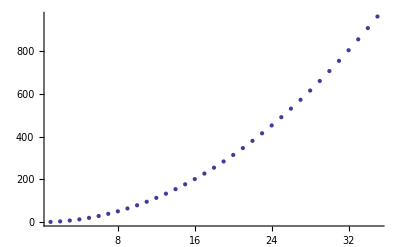

```mathematica
graph= ErrorBarPlots`ErrorListPlot[data]
```

```mathematica
loglog=Table[{Log[N[i]],Log[data[[i,1]]],1/data[[i,1]]*data[[i,2]]},{i,1,Length[data]}];
```

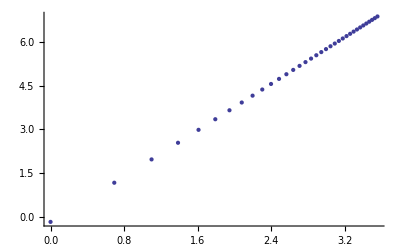

```mathematica
ListPlot[Table[{loglog[[i,1]],loglog[[i,2]]},{i,1,Length[loglog]}]]
```

### Fit

Using w_i = 1/Δi^2, from Taylor.

```mathematica
weights=Table[1/(loglog[[i,3]]^2),{i,1,Length[loglog]}];
```

This is also from Taylor, used below

```mathematica
Delta=Sum[weights[[i]],{i,Length[weights]}]*Sum[weights[[i]]*loglog[[i,1]]^2,{i,Length[loglog]}]-(Sum[weights[[i]]*loglog[[i,1]],{i,Length[loglog]}])^2;
```

More symbols to make expressions less unweildy.

```mathematica
x[i_]:=loglog[[i,1]];
y[i_]:=loglog[[i,2]];
w[i_]:=weights[[i]];
```

Now, the fit coefficients (for line off form y = A + Bx):

```mathematica
A=1/Delta(Sum[w[i]*x[i]^2,{i,Length[data]}]*Sum[w[i]*y[i],{i,Length[data]}]-Sum[w[i]*x[i],{i,Length[data]}]*Sum[w[i]*x[i]*y[i],{i,Length[data]}])
```

-0.229468

```mathematica
B=1/Delta(Sum[w[i],{i,Length[data]}]*Sum[w[i]*x[i]*y[i],{i,Length[data]}]-Sum[w[i]*x[i],{i,Length[data]}]*Sum[w[i]*y[i],{i,Length[data]}])
```

1.9963

Again, not quite quadratic. We can plot both:

```mathematica
F[x_]:=A+B*x
```

```mathematica
Needs["ErrorBarPlots`"]
```

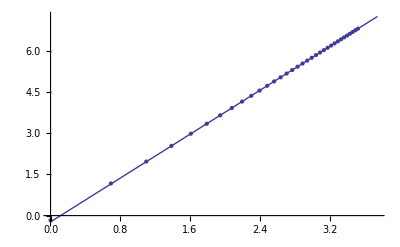

```mathematica
Show[Plot[F[x],{x,0,3.75}],ErrorListPlot[Table[{{x[i],y[i]},ErrorBar[loglog[[i,3]]]},{i,1,34}]]]
```

Uncertainties in A and B:

```mathematica
σA=Sqrt[Sum[w[i]*x[i]^2,{i,Length[loglog]}]/Delta]
```

0.00013847

```mathematica
σB=Sqrt[Sum[w[i],{i,Length[loglog]}]/Delta]
```

0.0000539865

Checking the goodness of the fit:

```mathematica
fitvals=Table[F[loglog[[i,1]]],{i,1,Length[loglog]}];
```

```mathematica
residuals=Table[fitvals[[i]]-loglog[[i,2]],{i,1,Length[loglog]}];
```

This expression should output a list of booleans. TRUE means that the fit is inside the error bars (resdiual < error bar) and FALSE means it’s outside

```mathematica
Table[Abs[residuals[[i]]]<loglog[[i,3]],{i,1,33}]
```

{False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

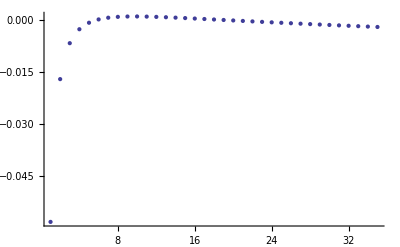

```mathematica
ListPlot[residuals]
```

```mathematica
?FindFit
```

FindFit[data,expr,pars,vars] finds numerical values of the parameters pars that make expr give a best fit to data as a function of vars. The data can have the form {{x_1,y_1,…,f_1},{x_2,y_2,…,f_2},…}, where the number of coordinates x, y, … is equal to the number of variables in the list vars. The data can also be of the form {f_1,f_2,…}, with a single coordinate assumed to take values 1, 2, …. 
FindFit[data,{expr,cons},pars,vars] finds a best fit subject to the parameter constraints cons.

```mathematica
quadfit=FindFit[Table[data[[i,1]],{i,1,Length[data]}],a x^2+b x +c,{a,b,c},x]
```

{a→0.786088,b→0.00118845,c→0.107507}

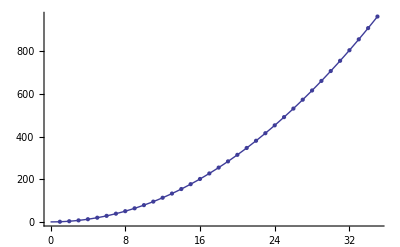

```mathematica
Show[graph,Plot[a x^2+b x+c/.quadfit,{x,0,Length[data]}]]
```

```mathematica
F[x_]=a x^2 +b x + c /.quadfit
```

0.107507+0.00118845 x+0.786088 x^2

```mathematica
fitvals=Table[F[i],{i,1,Length[data]}];
```

```mathematica
residuals=Table[fitvals[[i]]-data[[i,1]],{i,1,Length[data]}];
```

```mathematica
Table[Abs[residuals[[i]]]<data[[i,2]],{i,1,Length[data]}]
```

{False,False,False,True,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}